```mathematica
f[x_]= UnitStep[x]
```

UnitStep[x]

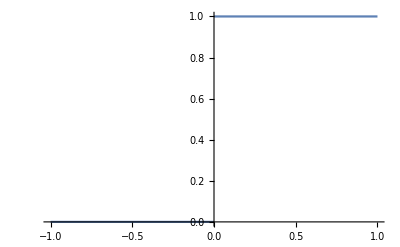

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
c[n_]:=c[n]=NIntegrate[1 LegendreP[n,x],{x,0,1}]/(2/(2n+1))
```

```mathematica
Table[c[n],{n,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.925766}. NIntegrate obtained -1.47451×10^-17 and 4.02883×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.79352×10^-8}. NIntegrate obtained -1.34441×10^-17 and 7.45705×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999998206481784018499997731624644344006203056096637737937271595}. NIntegrate obtained 1.73472×10^-17 and 2.97497×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.5,0.75,-3.68629×10^-17,-0.4375,-6.04985×10^-17,0.34375,1.12757×10^-16,-0.292969,8.29415×10^-16,0.259766,8.19657×10^-16}

```mathematica
fapprox[x_,M_]:= Sum[c[n] LegendreP[n,x],{n,0,M}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.914047}. NIntegrate obtained -5.29201×10^-13 and 6.80029×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.923813}. NIntegrate obtained 3.42602×10^-11 and 3.21166×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained -1.27501×10^-10 and 1.01928×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

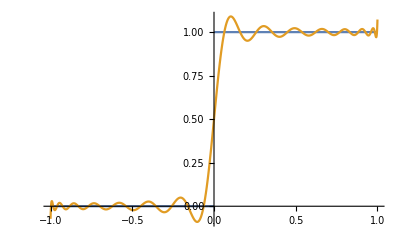

```mathematica
Plot[{f[x],fapprox[x,30]}//Evaluate,{x,-1,1}]
```

```mathematica
error[x_,M_]:= f[x]-fapprox[x,M]
```

```mathematica
Table[Integrate[error[x,M]^2//Evaluate,{x,-1,1}],{M,5,30,5}]
```

$Aborted

```mathematica
Integrate[error[x,5]^2,{x,-1,1}]
```

0.0488281

```mathematica
Integrate[error[x,15]^2,{x,-1,1}]
```

0.0192827

```mathematica
Integrate[error[x,20]^2,{x,-1,1}]
```

0.0155225

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,t_]= x T1/L Sin[ω t]
```

1/5 x Sin[t]

```mathematica
ψ[n_,x_]= Sin[n Pi x/L]
```

Sin[(n π x)/L]

```mathematica
λ[n_]= -χ(n Pi/L)^2;
```

```mathematica
s[n_,t_] = -ω T1 Cos[ω t]/L Integrate[x ψ[n,x],{x,0,L}]/(L/2)
```

-(2 T1 ω Cos[t ω] (-n π Cos[n π]+Sin[n π]))/(n^2 π^2)

```mathematica
DSolve[f'[t]==λ[n] f[t] + s[n,t],f[t],t]
```

{{f[t]→ⅇ^(-(n^2 π^2 t χ)/L^2) C[1]+(2 L^2 T1 ω (n π Cos[n π]-Sin[n π]) (n^2 π^2 χ Cos[t ω]+L^2 ω Sin[t ω]))/(n^2 π^2 (n^4 π^4 χ^2+L^4 ω^2))}}

```mathematica
f[n_,t_]=(f[t]/.%[[1]])/.C[1]->a[n]
```

ⅇ^(-(n^2 π^2 t χ)/L^2) a[n]+(2 L^2 T1 ω (n π Cos[n π]-Sin[n π]) (n^2 π^2 χ Cos[t ω]+L^2 ω Sin[t ω]))/(n^2 π^2 (n^4 π^4 χ^2+L^4 ω^2))

```mathematica
f[n,0]
```

a[n]+(2 L^2 T1 χ ω (n π Cos[n π]-Sin[n π]))/(n^4 π^4 χ^2+L^4 ω^2)

```mathematica
Solve[%==0,a[n]]
```

{{a[n]→-(2 L^2 T1 χ ω (n π Cos[n π]-Sin[n π]))/(n^4 π^4 χ^2+L^4 ω^2)}}

```mathematica
f[n_,t_]= f[n,t]/.%[[1]];
```

```mathematica
f[n,0]
```

0

```mathematica
ΔT[x_,t_]= Sum[f[n,t] ψ[n,x],{n,1,10}];
```

```mathematica
T[x_,t_]= u[x,t] + ΔT[x,t];
```

```mathematica
L=5; χ=.5; ω=1; T1=1;
```

```mathematica
T[.1,.2]
```

0.0164549

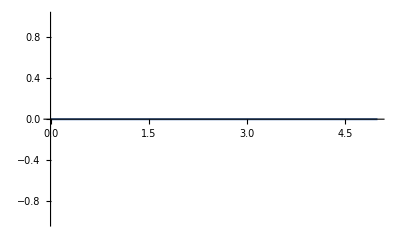
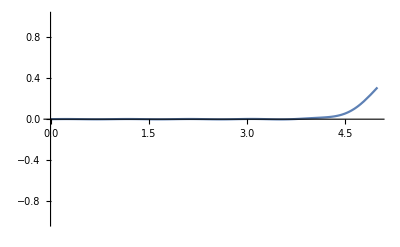
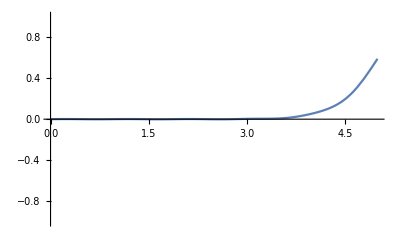
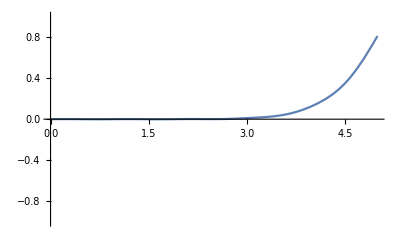
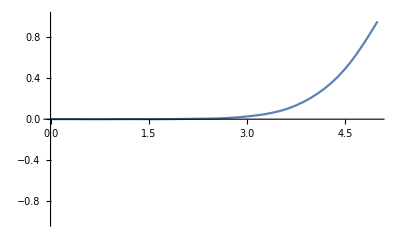
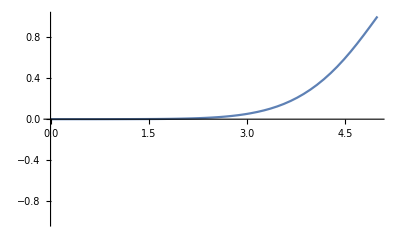
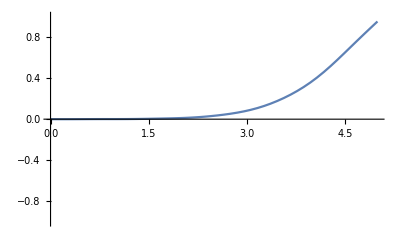
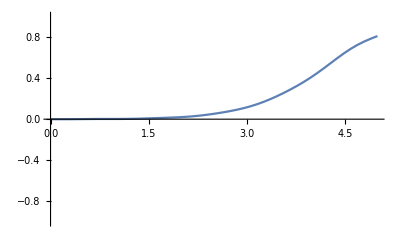

```mathematica
Table[Plot[T[x,t],{x,0,L},PlotRange->{-1,1}],{t,0,4Pi,.1Pi}]
```

```mathematica
ListAnimate[%]
```